```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->200{1,1}];
```

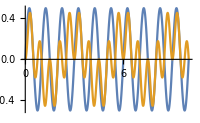

```mathematica
tmax=10;
v[t_,T1_,T2_]:= (1/2 Sin[2 π t/T1])Sin[2 π t/T2]
u[t_,T1_]:= (1/2 Sin[2 π t/T1])
multi=Table[N[v[τ,1,1.5]],{τ,0,tmax,.1}];
single=Table[N[u[τ,1]],{τ,0,tmax,.1}];
Plot[{N[u[τ,1]],N[v[τ,1,1.5]]},{τ,0,tmax}]
```

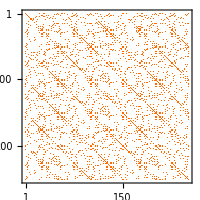
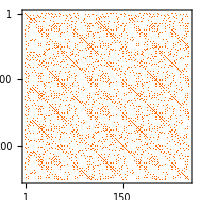
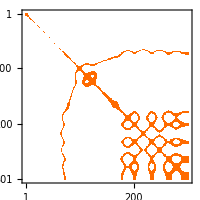
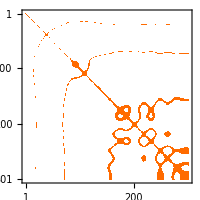
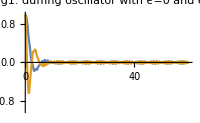

```mathematica
Module[{tmax=60,ϵ,δ=1,γ=1,T1=1,T2=10},
ϵ=0;
duffing0=NDSolveValue[{ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Sin[2 π t/T1]Sin[2 π t/T2],y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=10;
duffing5=NDSolveValue[{ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Sin[2 π t/T1]Sin[2 π t/T2],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[{duffing0[t],duffing5[t]},{t,0.,tmax},PlotLabel->"Fig1. duffing oscillator with ϵ=0 and ϵ=5",PlotRange->{{0,tmax},{-1,1}},PlotLegends->{"ϵ=0","ϵ=5"}]

With[{stepSize=1/30,end=10,nn=0.0001},MatrixPlot[UnitStep[nn-DistanceMatrix[duffing0[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[duffing5[Range[0,end,stepSize]]]]]
]

With[{stepSize=0.2,end=tmax,nn=0.00001},MatrixPlot[UnitStep[nn-DistanceMatrix[duffing0[Range[10,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[duffing5[Range[10,end,stepSize]]]]]
]
]
```